```mathematica
Do[
v=8;
vv=ToString[v];
ll=ToString[l];

ChR4[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-normalized-10.txt",{Number,Number}];
ChRt4[v][l]=ReadList["/Users/ashkanbalouchi/Desktop/Traffic/TrafficSim2/Gap/V9/fine/v"<>vv<>"-l"<>ll<>"k-susceptibility-time-top-10.txt",{Number,Number}];



iR4[v][l]=Interpolation[ChR4[v][l]];
iRt4[v][l]=Interpolation[ChRt4[v][l]];

,{l,{2,5,10,20,40,60,80,100}}]
```

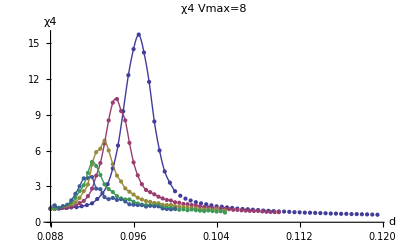

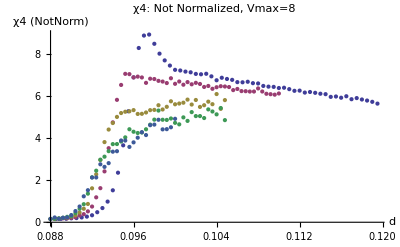

```mathematica
v=8;
picR1=ListPlot[{ChR4[v][2],ChR4[v][5],ChR4[v][10],ChR4[v][20],ChR4[v][40]},PlotRange->Full,PlotLabel->"χ4 Vmax=8",AxesLabel->{"d","χ4"}];
picR2=Plot[{iR4[v][2][i],iR4[v][5][i],iR4[v][10][i],iR4[v][20][i],iR4[v][40][i]},{i,0.088,0.1},PlotRange->Full];
picR3=ListPlot[{ChRt4[v][2],ChRt4[v][5],ChRt4[v][10],ChRt4[v][20],ChRt4[v][40]},PlotRange->Full,PlotLabel->"χ4: Not Normalized, Vmax=8",AxesLabel->{"d","χ4 (NotNorm)"}];
picR4=Plot[{iRt4[v][2][i],iRt4[v][5][i],iRt4[v][10][i],iRt4[v][20][i],iRt4[v][40][i]},{i,0.065,0.077},PlotRange->Full];
Show[{picR1,picR2}]
Show[{picR3,picR4}]
```

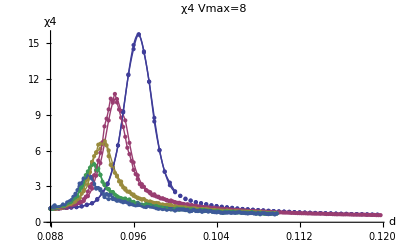

```mathematica
Show[{picR1,picR2,pic1,pic2}]
```

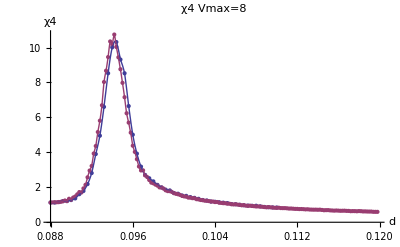

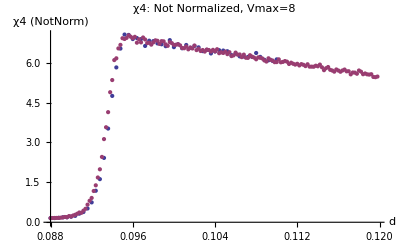

```mathematica
v=8;
l=5;
picR1=ListPlot[{ChR4[v][l],Ch4[v][l]},PlotRange->Full,PlotLabel->"χ4 Vmax=8",AxesLabel->{"d","χ4"}];
picR2=Plot[{iR4[v][l][i],i4[v][l][i]},{i,0.088,0.1},PlotRange->Full];
picR3=ListPlot[{ChRt4[v][l],Cht4[v][l]},PlotRange->Full,PlotLabel->"χ4: Not Normalized, Vmax=8",AxesLabel->{"d","χ4 (NotNorm)"}];
picR4=Plot[{iRt4[v][2][i],it4[v][l][i]},{i,0.065,0.077},PlotRange->Full];
Show[{picR1,picR2}]
Show[{picR3,picR4}]
```